```mathematica
l={0,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0}
```

{0,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0}

```mathematica
Total[l[[;;#]]]&/@Range[Length[l]]
```

{0,1,2,3,3,3,3,4,4,4,4,4,5,5,5,6,6,6,6,7,7,7,8,8}

```mathematica
%/Range[Length[l]]
```

{0,1/2,2/3,3/4,3/5,1/2,3/7,1/2,4/9,2/5,4/11,1/3,5/13,5/14,1/3,3/8,6/17,1/3,6/19,7/20,1/3,7/22,8/23,1/3}

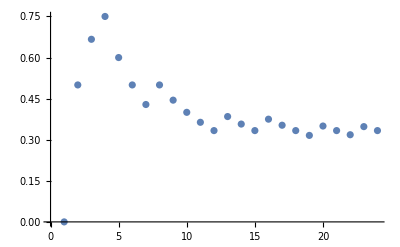

```mathematica
%//ListPlot
```